```mathematica
Quit[]
```

# Calculations

```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

Calculations

## Initial constants

```mathematica
Y=1/2;
Gf=1.166*10^(-5);
dm232=1;
a1=1.07;
Fm2320=1/(3*π);
mπ=0.13957;
fπ=0.1304;
mρ=0.7665;
fρ=0.216;
ma1=1.230;
fa1=0.238;
SetAttributes[V,Orderless];
V["c","b"]=0.0411;V["c","s"]=0.974;V["c","d"]=0.225;
V["u","b"]=0.00357;V["u","s"]=0.225;V["u","d"]=0.974;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Fq2π=ReadList["plot2pi.txt",{Number,Number}];
Fq3π=ReadList["plot3pi.txt",{Number,Number}];
Fq4π=ReadList["plot4pi.txt",{Number,Number}];
Fq5π=ReadList["plot5pi.txt",{Number,Number}];
```

## Initial Tau lepton calculations for constants

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p1,p2]=(m1^2+m2^2-q2)/2;
q=p1-p2;
H =SpinorUBar[p2,m2].GA[μ].(1+GA[5]).SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
H2=H*cH;
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[q,μ]*FV[q,α]-q2*MT[μ,α])]];
λ:=√(1-((m2+√q2)/m1)^2)*√(1-((m2-√q2)/m1)^2);
HT:=λ*H4;
m1=1.776;
m2=0;
h=6.5*10^-25;τ=290*10^-15;
Γτ=h/τ;
```

```mathematica
(*Decay to 2π*)
Clear[Br, BrNorm];
BrNorm=0.2549;
dΓ2π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq2π][q2];
Γ2π=NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Const2π=BrNorm/Br
Γ2π=Const2π*NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Error=Br/BrNorm
```

0.35257

1.

```mathematica
(*Decay to 3π*)
Clear[Br, BrNorm];
BrNorm=0.0903;
dΓ3π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq3π][q2];
Γ3π=NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Const3π=BrNorm/Br
Γ3π=Const3π*NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Error=Br/BrNorm
```

7.00952

1.

```mathematica
(*Decay to 4π*)
Clear[Br, BrNorm];
BrNorm=0.0462;
dΓ4π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq4π][q2];
Γ4π=NIntegrate[dΓ4π, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4π/Γτ;
Const4π=BrNorm/Br
Γ4π=Const4π*NIntegrate[dΓ4π, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4π/Γτ;
Error=Br/BrNorm
```

10856.9

1.

```mathematica
(*Decay to 5π*)
Clear[Br, BrNorm];
BrNorm=0.000769;
dΓ5π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq5π][q2];
Γ5π=NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
Const5π=BrNorm/Br
Γ5π=Const5π*NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
Error=Br/BrNorm
```

32919.5

1.

## Clear

```mathematica
Clear[Γ2π,Γ3π,Γ4π,Γ5π,dΓ2π,dΓ3π,dΓ4π,dΓ5π,H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ClearScalarProducts;
```

## Init

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,m232,q,m1,m2,m3,m4,Br,f1,f2,g1,g2];
ScalarProduct[p11,p11]=m1^2;
ScalarProduct[p22,p22]=m2^2;
ScalarProduct[p11,p22]=(m1^2+m2^2-m232)/2;
SetMandelstam[m232,m132,m122,p1,-p2,-pe,-ke,m1,m2,0,0];
qq=p11-p22;
q=p1-p2;
sigma=I*(GA[μ].GA[ν]-GA[ν].GA[μ])/2;
H =SpinorUBar[p22,m2].(GA[μ]*f1+I*sigma*FV[qq,ν]*f2/m1).SpinorU[p11, m1]-SpinorUBar[p22,m2].(GA[μ]*g1+ⅈ*sigma*FV[qq,ν]*g2/m1).GA[5].SpinorU[p11, m1];
HH=SpinorUBar[p2,m2].(GA[μ]*f1+I*sigma*FV[q,ν]*f2/m1).SpinorU[p1, m1]-SpinorUBar[p2,m2].(GA[μ]*g1+ⅈ*sigma*FV[q,ν]*g2/m1).GA[5].SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
cHH= ComplexConjugate[HH]/.{μ->α,ν->β};
H2=H*cH;
HH2=HH*cHH;
HH3=DiracSimplify[FermionSpinSum[HH2]]/.{DiracTrace->TR};
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α]-m232*MT[μ,α])]];
λ:=√(1-((m2+√m232)/m1)^2)*√(1-((m2-√m232)/m1)^2);
HT:=λ*H4;
(*T=Transversal*)
HL:=λ*Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α])]];
(*L=Longitudinal*)
L=SpinorUBar[pe].GA[μ].(1+GA[5]).SpinorV[ke];
cL=ComplexConjugate[L]/.{μ->α};
L2=FermionSpinSum[L*cL]/.{DiracTrace->TR};
M2=Simplify[1/2*Gf^2*Calc[HH3*L2]];
M3=M2//.m132->m1^2+m2^2-m122-m232;
E2ZV= (m122-m2^2 +m3^2)/(2*Sqrt[m122]) (*  E2^*  *);
E3ZV= (m1^2-m122-m4^2)/(2*Sqrt[m122])  (*  E3^*  *);
m23min=(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]+Sqrt[E3ZV^2-m4^2])^2;
m23max=Simplify[Calc[(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]-Sqrt[E3ZV^2-m4^2])^2]];
m12min=m2^2;
m12max=m1^2;
```

```mathematica
Clear[Fq2πb,Fq3πb,Fq4πb,Fq5πb,dΓ2πb, dΓ3πb, dΓ4πb, dΓ5πb];
dΓl:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*dm232 /(2*π)*(1/(8*π))*Vckm^2*HT*Fm2320
dΓl1:=(1/2)*(1/(2*π)^3)*(1/(32*m1^3))*Vckm^2*M3;
dΓ2π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const2π*Interpolation[Fq2π][m232];
dΓ3π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const3π*Interpolation[Fq3π][m232];
dΓ4π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const4π*Interpolation[Fq4π][m232];
dΓ5π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const5π*Interpolation[Fq5π][m232];
```

## File

```mathematica
SetDirectory[NotebookDirectory[]];
<<"wang_data.m";
decays={#["in"],#["out"]}&/@Normal[DeleteDuplicates[dsFF[All,{"in","out"}]]];
Clear[$FF];
$FF[data_]:=Module[{},Switch[data["func"],"FF",Return[data["F0"]/(1-m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];,"GG",Return[data["F0"]/(1+m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];];];
(*Clear[cS,cA];*)
Clear[FF];
FF[query_]:=Module[{$res},$res=dsFF[query];
Return[cS $FF[$res[1]]+cA $FF[$res[2]]]];
```

## Test

```mathematica
in="\\Omega_{cc}^{+}";
out="\\Omega_{c}^{0}";
testresult={};
AppendTo[testresult,{"in","out","Vckm","l nul","pi" ,"rho/2pi","2pi/2pi_before", "3pi/3pi_before", "4pi/4pi_before", "5pi/5pi_before"}];
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*Vckm^2*Hπ;
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γa1=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\a_1"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,4mπ^2,(m1-m2)^2}];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ4π=NIntegrate[dΓ4π, {m232,16mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[testresult,{in,out,Vckm1->Vckm2,Floor[Chop[Γl1/fullΓ],-0.000001]*100,Floor[Chop[Γπ/fullΓ],-0.0000000001]*100,Floor[Chop[Γρ/Γ2π],-0.00000001],Floor[Chop[Γ2π/fullΓ],-0.0000001]*100,Floor[Chop[Γ3π/fullΓ],-0.0000001]*100,Floor[Chop[Γ4π/fullΓ],-0.0000001]*100,Floor[Chop[Γ5π/fullΓ],-0.0000001]*100}];
AppendTo[testresult,{in,out,m1-m2,Vckm1->Vckm2,1,1,1,1,1,1,1}];
testresult
```

{{in,out,m1-m2,Vckm,l nul,pi,rho/2pi,2pi/2pi_before,3pi/3pi_before,4pi/4pi_before,5pi/5pi_before},{\Omega_{cc}^{+},\Omega_{c}^{0},c→s,6.6604,6.49593,1.33644,16.8782,0.26464,0.00601,0.00001},{\Omega_{cc}^{+},\Omega_{c}^{0},0.955,c→s,1,1,1,1,1,1,1}}

## Main calculation

```mathematica
result={};
AppendTo[result,{"in","out","Vckm","l nul","pi" ,"rho/2pi","2pi", "3pi", "4pi", "5pi"}];
i=.0;
PrintTemporary[Dynamic[dec],"Завершено",Dynamic[Floor[i/36*100,-0.1]], "%" ];
Do[
{in,out}=dec;
i=i+1;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*Vckm^2*Hπ;
Ha1=HT/.{m232-> ma1^2};
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,4mπ^2,(m1-m2)^2}];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ4π=NIntegrate[dΓ4π, {m232,16mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[result,{in,out,Vckm1->Vckm2,Floor[Chop[Γl1/fullΓ],-0.000001]*100,Floor[Chop[Γπ/fullΓ],-0.0000000001]*100,Floor[Chop[Γρ/Γ2π],-0.00000001],Floor[Chop[Γ2π/fullΓ],-0.0000001]*100,Floor[Chop[Γ3π/fullΓ],-0.0000001]*100,Floor[Chop[Γ4π/fullΓ],-0.0000001]*100,Floor[Chop[Γ5π/fullΓ],-0.0000001]*100}];
,{dec,decays}];
result
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m232} = TraditionalForm`{0.04309}. NIntegrate obtained TraditionalForm`6.199949246656747`*^-14 and TraditionalForm`2.7953540267495105`*^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`18 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m122, m232} = TraditionalForm`{0.468141, 0.0332227}. NIntegrate obtained TraditionalForm`6.200280512010538`*^-14 and TraditionalForm`5.231484967839733`*^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m232} = TraditionalForm`{0.0429364}. NIntegrate obtained TraditionalForm`6.139831083689381`*^-14 and TraditionalForm`2.321958443411979`*^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

(in | out | Vckm | l nul | pi | rho/2pi | 2pi/2pi_before | 3pi/3pi_before | 4pi/4pi_before | 5pi/5pi_before
\Xi_{cc}^{++} | \Lambda_{c}^{+} | c→d | 0.4936 | 0.220173 | 1.15032 | 0.86341 | 0.20795 | 0.05086 | 0.00022
\Xi_{cc}^{++} | \Sigma_{c}^{+} | c→d | 0.4503 | 0.175318 | 1.16625 | 0.89963 | 0.15367 | 0.01701 | 0.00004
\Xi_{cc}^{++} | \Xi_{c}^{+} | c→s | 4.9858 | 4.84398 | 1.2266 | 10.0496 | 0.63392 | 0.04257 | 0.00006
\Xi_{cc}^{++} | \Xi_{c}^{\prime+} | c→s | 5.975 | 4.02341 | 1.24937 | 14.0915 | 0.7253 | 0.02891 | 0.00003
\Xi_{cc}^{+} | \Sigma_{c}^{0} | c→d | 0.2988 | 0.116762 | 1.16683 | 0.5978 | 0.10132 | 0.01113 | 0.00003
\Xi_{cc}^{+} | \Xi_{c}^{0} | c→s | 1.6513 | 1.60429 | 1.2266 | 3.32834 | 0.20995 | 0.0141 | 0.00002
\Xi_{cc}^{+} | \Xi_{c}^{\prime0} | c→s | 1.984 | 1.34129 | 1.25011 | 4.68409 | 0.23845 | 0.00944 | 0.00001
\Omega_{cc}^{+} | \Xi_{c}^{0} | c→d | 0.2079 | 0.171207 | 1.21767 | 0.42059 | 0.03418 | 0.0028 | 0.00001
\Omega_{cc}^{+} | \Xi_{c}^{\prime0} | c→d | 0.2492 | 0.14169 | 1.23155 | 0.57731 | 0.03896 | 0.00185 | 0.00001
\Omega_{cc}^{+} | \Omega_{c}^{0} | c→s | 6.6604 | 6.49593 | 1.33644 | 16.8782 | 0.26464 | 0.00601 | 0.00001
\Xi_{bb}^{0} | \Sigma_{b}^{+} | b→u | 0.0043 | 7.7×10^-7 | 1.02313 | 0.00043 | 0.00038 | 0.00079 | 0.00128
\Xi_{bb}^{0} | \Xi_{bc}^{+} | b→c | 2.5911 | 0.00197928 | 1.05065 | 0.54037 | 0.39867 | 0.66891 | 0.11346
\Xi_{bb}^{0} | \Xi_{bc}^{\prime+} | b→c | 1.1503 | 0.00032846 | 1.02227 | 0.12499 | 0.11273 | 0.23846 | 0.04995
\Xi_{bb}^{-} | \Lambda_{b}^{0} | b→u | 0.0011 | 4.8×10^-7 | 1.04512 | 0.00022 | 0.00017 | 0.00027 | 0.00031
\Xi_{bb}^{-} | \Sigma_{b}^{0} | b→u | 0.0022 | 3.9×10^-7 | 1.02314 | 0.00022 | 0.00019 | 0.0004 | 0.00065
\Xi_{bb}^{-} | \Xi_{bc}^{0} | b→c | 2.6207 | 0.00198664 | 1.05062 | 0.54437 | 0.40173 | 0.6746 | 0.11458
\Xi_{bb}^{-} | \Xi_{bc}^{\prime0} | b→c | 1.1556 | 0.00032685 | 1.02224 | 0.12488 | 0.11266 | 0.23857 | 0.05005
\Omega_{bb}^{-} | \Xi_{b}^{0} | b→u | 0.002 | 9.5×10^-7 | 1.04525 | 0.00044 | 0.00033 | 0.00054 | 0.00047
\Omega_{bb}^{-} | \Xi_{b}^{\prime0} | b→u | 0.0044 | 7.7×10^-7 | 1.02321 | 0.00045 | 0.0004 | 0.00082 | 0.00134
\Omega_{bb}^{-} | \Omega_{bc}^{0} | b→c | 4.8074 | 0.00399701 | 1.0512 | 1.07854 | 0.79206 | 1.30849 | 0.21616
\Omega_{bb}^{-} | \Omega_{bc}^{\prime0} | b→c | 2.1266 | 0.00065815 | 1.02197 | 0.25058 | 0.22639 | 0.47228 | 0.09663
\Xi_{bc}^{+} | \Lambda_{b}^{0} | c→d | 0.2234 | 0.0255156 | 1.17132 | 0.41499 | 0.07805 | 0.01482 | 0.00005
\Xi_{bc}^{+} | \Sigma_{b}^{0} | c→d | 0.1483 | 0.0173712 | 1.2145 | 0.33162 | 0.02915 | 0.00173 | 0.00001
\Xi_{bc}^{+} | \Xi_{b}^{0} | c→s | 2.3 | 0.539987 | 1.23726 | 4.71893 | 0.24847 | 0.0141 | 0.00002
\Xi_{bc}^{0} | \Sigma_{b}^{-} | c→d | 0.1121 | 0.0132396 | 1.21583 | 0.25129 | 0.02167 | 0.00127 | 0.00001
\Xi_{bc}^{0} | \Xi_{b}^{-} | c→s | 0.8684 | 0.205536 | 1.23795 | 1.78221 | 0.09218 | 0.00515 | 0.00001
\Omega_{bc}^{0} | \Xi_{b}^{-} | c→d | 0.2542 | 0.0223417 | 1.15361 | 0.44309 | 0.1046 | 0.02499 | 0.00011
\Omega_{bc}^{0} | \Omega_{b}^{-} | c→s | 6.0272 | 0.710781 | 1.222 | 13.588 | 1.06522 | 0.058 | 0.00007
\Xi_{bc}^{+} | \Sigma_{c}^{++} | b→u | 0.0035 | 1.5×10^-6 | 1.0274 | 0.00024 | 0.00021 | 0.00045 | 0.0016
\Xi_{bc}^{+} | \Xi_{cc}^{++} | b→c | 1.5843 | 0.00464738 | 1.05753 | 0.41395 | 0.28927 | 0.45099 | 0.07028
\Xi_{bc}^{0} | \Lambda_{c}^{+} | b→u | 0.0003 | 3.×10^-7 | 1.04836 | 0.00005 | 0.00004 | 0.00006 | 0.00016
\Xi_{bc}^{0} | \Sigma_{c}^{+} | b→u | 0.0007 | 2.9×10^-7 | 1.0274 | 0.00005 | 0.00004 | 0.00009 | 0.00031
\Xi_{bc}^{0} | \Xi_{cc}^{+} | b→c | 0.6027 | 0.00176777 | 1.05753 | 0.15746 | 0.11004 | 0.17155 | 0.02674
\Omega_{bc}^{0} | \Xi_{c}^{+} | b→u | 0.0005 | 5.5×10^-7 | 1.04771 | 0.00009 | 0.00007 | 0.00011 | 0.00026
\Omega_{bc}^{0} | \Omega_{cc}^{+} | b→c | 1.8684 | 0.00383858 | 1.05534 | 0.40678 | 0.28946 | 0.47062 | 0.07842)

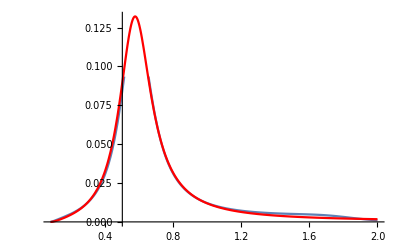

```mathematica
Show[Plot[Fq2π,{m232, 4mpi^2, 2}], PlotRange-> All]
```